```mathematica
SetDirectory["/Users/deddu/Documents/workspace/MLtests/misc"]
```

/Users/deddu/Documents/workspace/MLtests/misc

```mathematica
read_stats[fname_]:=Reverse[Flatten[Import[fname]]];
```

```mathematica
llplot[_what]:= ListLogLogPlot[what/10000,PlotRange->{{1,Length[what]},{0,1}},PlotStyle->{Thick,Darker[Red]}]
```

```mathematica
DefaultLabelStyle->Directive[FontFamily->"Helvetica"]
```

DefaultLabelStyle→Directive[FontFamily→Helvetica]

```mathematica
DefaultTicksStyle -> Directive[ Thick,15]
```

DefaultTicksStyle→Directive[Thickness[Large],15]

```mathematica
en1=Reverse[Flatten[Import["english_segmentation/en_stats_10.tsv"]]];
en2=Reverse[Flatten[Import["english_segmentation/en_stats_30.tsv"]]];
en3=Reverse[Flatten[Import["english_segmentation/en_stats_60.tsv"]]];
en4=Reverse[Flatten[Import["english_segmentation/en_stats_100.tsv"]]];
en5=Reverse[Flatten[Import["english_segmentation/en_stats_200.tsv"]]];
en6=Reverse[Flatten[Import["english_segmentation/en_stats_400.tsv"]]];
```

```mathematica
fg1 = Reverse[Flatten[Import["fg_smarts_stats.tsv"]]];
```

```mathematica
d1=Reverse[Flatten[Import["smarts_stats_10.tsv"]]];
d2=Reverse[Flatten[Import["smarts_stats_30.tsv"]]];
d3=Reverse[Flatten[Import["smarts_stats_60.tsv"]]];
d4=Reverse[Flatten[Import["smarts_stats_100.tsv"]]];
d5=Reverse[Flatten[Import["smarts_stats_200.tsv"]]];
d6=Reverse[Flatten[Import["smarts_stats_400.tsv"]]];
```

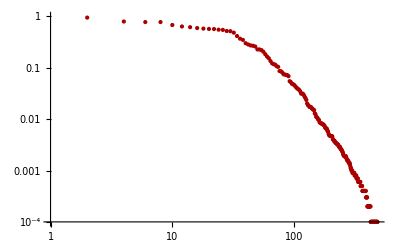

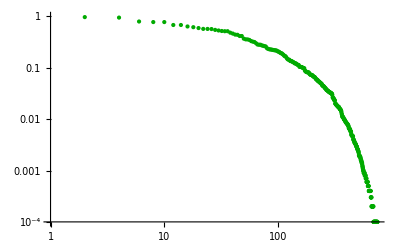

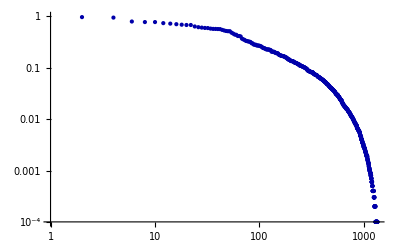

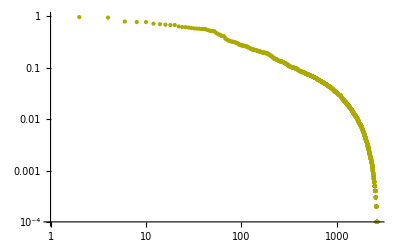

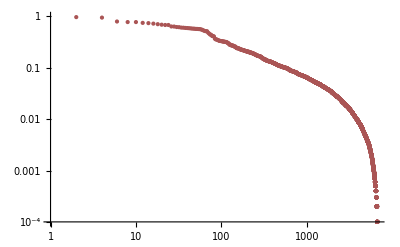

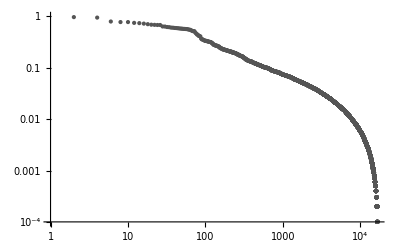

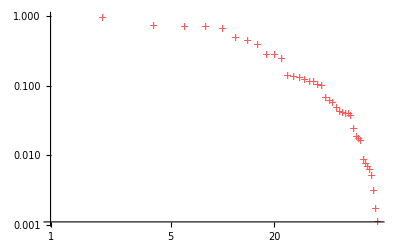

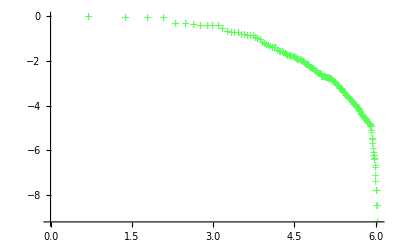

```mathematica
pp1=ListLogLogPlot[d1/10000,PlotRange->{{1,Length[d1]},{0,1}},PlotStyle->{Thick,Darker[Red]},LabelStyle-> Directive[FontFamily->"Helvetica"], TicksStyle->Directive[ Thick,15]]
pp2=ListLogLogPlot[d2/10000,PlotRange->{{1,Length[d2]},{0,1}},PlotStyle->{Thick,Darker[Green]},LabelStyle-> Directive[FontFamily->"Helvetica"], TicksStyle->Directive[ Thick,15]]
pp3=ListLogLogPlot[d3/10000,PlotRange->{{1,Length[d3]},{0,1}},PlotStyle->{Thick,Darker[Blue]},LabelStyle-> Directive[FontFamily->"Helvetica"], TicksStyle->Directive[ Thick,15]]
pp4=ListLogLogPlot[d4/10000,PlotRange->{{1,Length[d4]},{0,1}},PlotStyle->{Thick,Darker[Yellow]},LabelStyle-> Directive[FontFamily->"Helvetica"], TicksStyle->Directive[ Thick,15]]
pp5=ListLogLogPlot[d5/10000,PlotRange->{{1,Length[d5]},{0,1}},PlotStyle->{Thick,Darker[Pink]},LabelStyle-> Directive[FontFamily->"Helvetica"], TicksStyle->Directive[ Thick,15]]
pp6=ListLogLogPlot[d6/10000,PlotRange->{{1,Length[d6]},{0,1}},PlotStyle->{Thick,Darker[Gray]},LabelStyle-> Directive[FontFamily->"Helvetica"], TicksStyle->Directive[ Thick,15]]
pe1=ListLogLogPlot[en1/10000,PlotRange->{{1,Length[en1]},{0,1}},PlotStyle->{Thick,Lighter[Red]},PlotMarkers->{"+"},LabelStyle-> Directive[FontFamily->"Helvetica"], TicksStyle->Directive[ Thick,15]]
pe2=ListLogLogPlot[en2/10000,PlotRange->{{1,Length[en2]},{0,1}},PlotStyle->{Thick,Lighter[Green]},PlotMarkers->{"+"},LabelStyle-> Directive[FontFamily->"Helvetica"], TicksStyle->Directive[ Thick,15]]
pe3=ListLogLogPlot[en3/10000,PlotRange->{{1,Length[en3]},{0,1}},PlotStyle->{Thick,Lighter[Blue]},PlotMarkers->{"+"},LabelStyle-> Directive[FontFamily->"Helvetica"], TicksStyle->Directive[ Thick,15]]
pe4=ListLogLogPlot[en4/10000,PlotRange->{{1,Length[en4]},{0,1}},PlotStyle->{Thick,Lighter[Yellow]},PlotMarkers->{"+"},LabelStyle-> Directive[FontFamily->"Helvetica"], TicksStyle->Directive[ Thick,15]]
pe5=ListLogLogPlot[en5/10000,PlotRange->{{1,Length[en5]},{0,1}},PlotStyle->{Thick,Lighter[Pink]},PlotMarkers->{"+"},LabelStyle-> Directive[FontFamily->"Helvetica"], TicksStyle->Directive[ Thick,15]]
pe6=ListLogLogPlot[en6/10000,PlotRange->{{1,Length[en6]},{0,1}},PlotStyle->{Thick,Lighter[Gray]},PlotMarkers->{"+"},LabelStyle-> Directive[FontFamily->"Helvetica"], TicksStyle->Directive[ Thick,15]]
```

```mathematica
Needs["PlotLegends`"]
```

```mathematica
Export["ChemistryAsALanguage_600.png",Show[pp6,pe6,pp5,pe5,pp4,pe4,pp3,pe3, pp2, pe2,FrameLabel->{"Rank","Frequency"},ImageSize->600,RotateLabel->True] ]
```

ChemistryAsALanguage_600.png

```mathematica
Show[pp6,pe6,pp2,pe2,pp3,pe3, pp4, pe4, pp5,pe5]
```

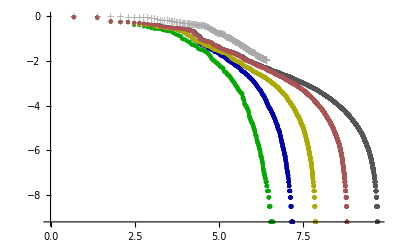

-Graphics-

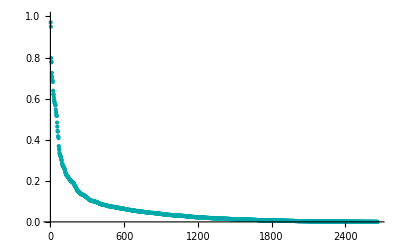

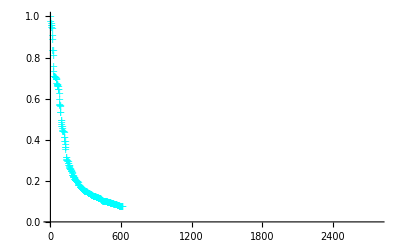

-Graphics-

-Graphics-

```mathematica
a=ListPlot[d4/10000,PlotRange->{{1,Length[d4]},{0,1}},PlotStyle->{Thick,Darker[Cyan]}, LabelStyle-> Directive[FontFamily->"Helvetica"]]
b=ListPlot[en4/10000,PlotRange->{{1,Length[en4]},{0,1}},PlotStyle->{Thick,Cyan},PlotMarkers->{"+"}, LabelStyle-> Directive[FontFamily->"Helvetica"]]
```

```mathematica
Show[a,b]
```

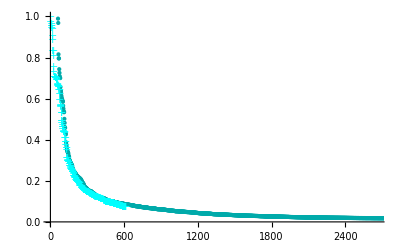

DefaultLabelStyleStyle→Directive[FontFamily→Helvetica]

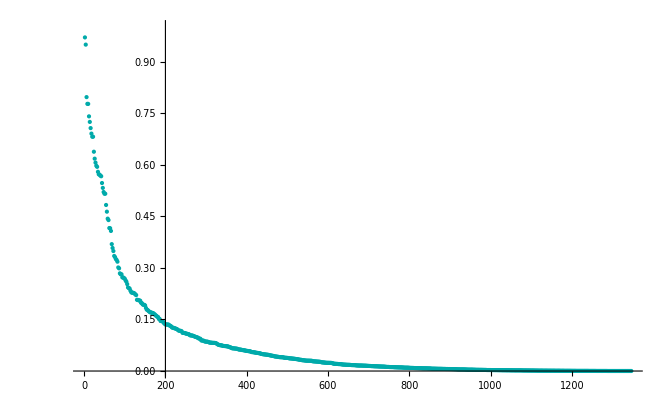

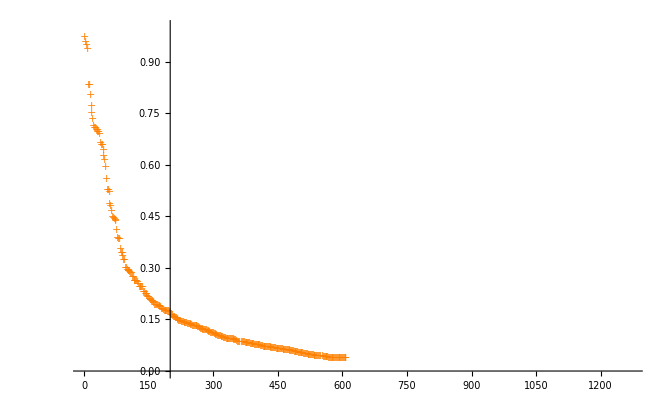

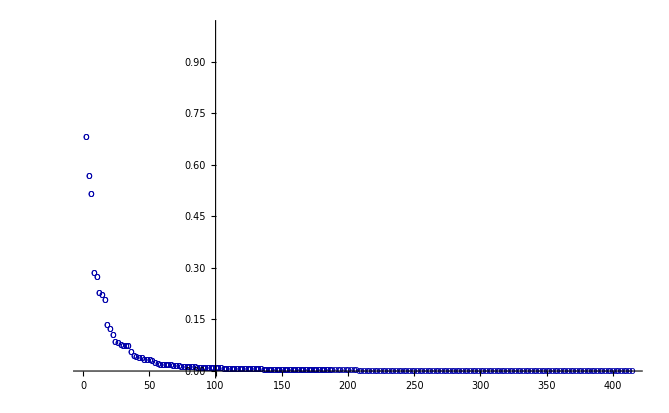

```mathematica
a=ListPlot[d3/10000,PlotRange->{{1,Length[d3]},{0,1}},PlotStyle->{Thick,Darker[Cyan]}, LabelStyle-> Directive[FontFamily->"Helvetica"]]
b=ListPlot[en3/10000,PlotRange->{{1,Length[en3]},{0,1}},PlotStyle->{Thick,Orange},PlotMarkers->{"+"}, LabelStyle-> Directive[FontFamily->"Helvetica"]]
c=ListPlot[fg1/10000,PlotRange->{{1,Length[fg1]},{0,1}},PlotStyle->{Thick,Darker[Blue]},PlotMarkers->{"o"}, LabelStyle-> Directive[FontFamily->"Helvetica"], TicksStyle->Directive[ Thick,15]]
```

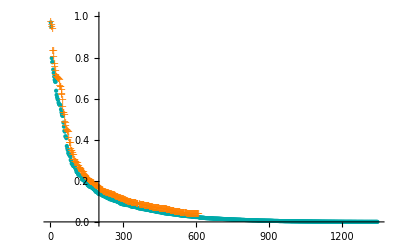

```mathematica
Show[a,b, c ]
```

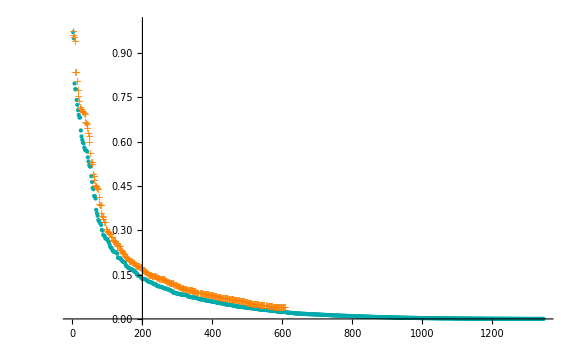

```mathematica
Show[%53,ImageSize->Large]
```

```mathematica
Show[%54,Method->{"AxesInFront"->False}]
```

-Graphics-

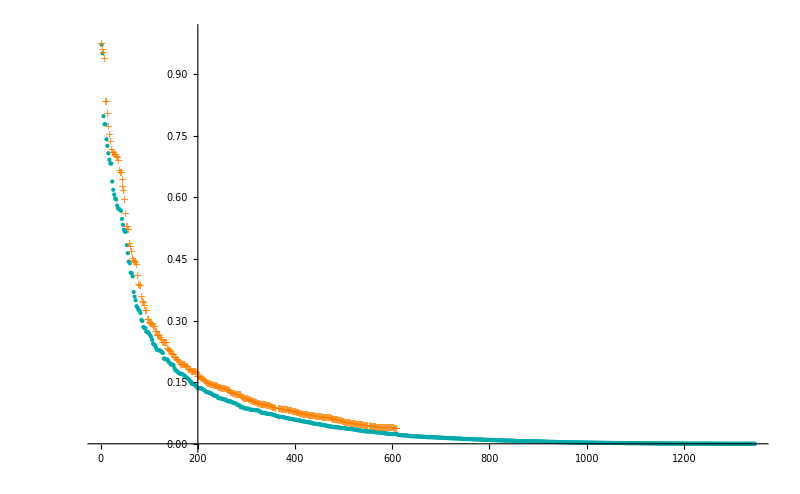

-Graphics-

```mathematica
Show[%55,ImageSize->{800,494},AspectRatio->Full]
```

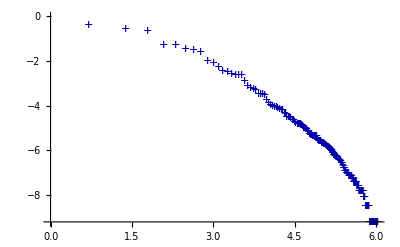

```mathematica
pfg=ListLogLogPlot[fg1/10000,PlotRange->{{1,Length[fg1]},{0,1}},PlotStyle->{Thick,Darker[Blue]},PlotMarkers->{"+"}]
```

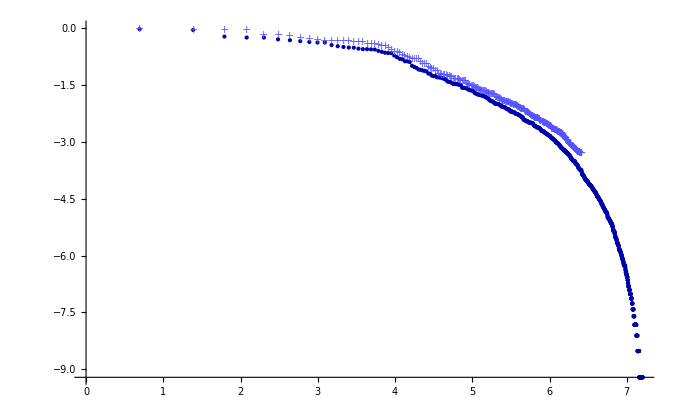

```mathematica
Show[pp3, pe3,pfg]
```